# Groundstate Energy and Bond Length of Carbon Monoxide CO

```mathematica
SetDirectory[NotebookDirectory[]];
<<../fermifab.m;
<<diatomic_base.m;
fermifabML=Install["../mlink/fermifabML/Windows-x86-64/fermifabML"];
```

```mathematica
<<PhysicalConstants`
```

```mathematica
(* experimental bond length of CO, in atomic units *)
Subscript[R, CO]=112.8 10^-12 Meter/BohrRadius
```

2.13161

```mathematica
(* average nuclear charge of a carbon and oxygen atom *)
Subscript[Z, CO]=(6+8)/2
```

7

```mathematica
(* nuclear charge difference *)
Subscript[ΔZ, CO]=8-6
```

2

```mathematica
(* quantum numbers *)
Subscript[m, l]=0;
Subscript[s, s]=0;
Subscript[m, s]=0;
```

```mathematica
paraInfo=ParaInfo[Subscript[ΔZ, CO]/Subscript[Z, CO]]⟦1;;10⟧;
```

```mathematica
QuantNumbersToString[#⟦1;;3⟧]&/@paraInfo
```

{1sσ,1pσ,2sσ,2pσ,1dσ,1p(+π),1p(-π),1d(+π),1d(-π),1fσ}

```mathematica
(* load precomputed integral tables *)
<<diatomic_coulomb_m0_zseries.m;
<<diatomic_coulomb_m1_zseries.m;
<<diatomic_coulomb_m2_zseries.m;
```

```mathematica
SymIntRule[ri_]:=Rule[First[ri],{First[ri],Outer[#+Transpose[#]&,Last[ri],2]}]
```

```mathematica
radinttables={SymIntRule/@radialIntM0TauZSeries,SymIntRule/@radialIntM1TauZSeries,SymIntRule/@radialIntM2TauZSeries};
```

## Calculate simultaneous LS eigenspaces

```mathematica
diatomicQuantLz=#⟦3⟧&/@paraInfo⟦;;10⟧
```

{0,0,0,0,0,1,-1,1,-1,0}

```mathematica
DiatomicAngularMomentumZ[]:=KroneckerProduct[SparseArray[DiagonalMatrix[diatomicQuantLz⟦3;;-1⟧]],IdentityMatrix[2]]
```

```mathematica
DiatomicSpinUp[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{0,1},{0,0}}]
DiatomicSpinDown[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{0,0},{1,0}}]
DiatomicSpinZ[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{1/2,0},{0,-1/2}}]
DiatomicSpin[length_]:=Module[{Su=DiatomicSpinUp[length],Sd=DiatomicSpinDown[length],Sz=DiatomicSpinZ[length]},{(Su+Sd)/2,-ⅈ(Su-Sd)/2,Sz}]
```

```mathematica
diorbnames=Flatten[Outer[#1<>#2&,QuantNumbersToString[#⟦1;;3⟧]&/@paraInfo⟦;;10⟧,{"↑","↓"}]]
Length[diorbnames]
```

{1sσ↑,1sσ↓,1pσ↑,1pσ↓,2sσ↑,2sσ↓,2pσ↑,2pσ↓,1dσ↑,1dσ↓,1p(+π)↑,1p(+π)↓,1p(-π)↑,1p(-π)↓,1d(+π)↑,1d(+π)↓,1d(-π)↑,1d(-π)↓,1fσ↑,1fσ↓}

20

```mathematica
(* diatomic CO molecule *)
diLz=PurgeSparseArray[p2N[DiatomicAngularMomentumZ[],16,1,10(*valence electrons*)]];
diS=PurgeSparseArray[p2N[#,16,1,10]]&/@DiatomicSpin[16];
diSS=PurgeSparseArray[Total[#.#&/@diS]];
```

```mathematica
(* check: diagonal matrix *)
PurgeSparseArray[diLz-DiagonalMatrix[Diagonal[diLz]]]
PurgeSparseArray[diS⟦3⟧-DiagonalMatrix[Diagonal[diS⟦3⟧]]]
```

SparseArray[<0>,{8008,8008}]

SparseArray[<0>,{8008,8008}]

```mathematica
(* indices of Subscript[L, z]-Subscript[S, z] eigevalues Subscript[m, l] and Subscript[m, s] *)
iZ=Intersection[Flatten[Position[Normal[Diagonal[diLz]],Subscript[m, l]]],Flatten[Position[Normal[Diagonal[diS⟦3⟧]],Subscript[m, s]]]];
Length[iZ]
```

824

```mathematica
(* short test *)
diS⟦3⟧⟦First[iZ],First[iZ]⟧
```

0

```mathematica
(* parity not conserved, but we use it to order basis *)
diatomicParitySpatial=(-1)^(#⟦2⟧)&/@paraInfo
DiatomicParity[]:=Flatten[KroneckerProduct[diatomicParitySpatial⟦3;;-1⟧,{1,1}]]
Times@@(DiatomicParity[]⟦FermiToCoords[#]⟧)&/@FermiMap[16,10];
{iEven,iOdd}={Flatten[Position[%,1]],Flatten[Position[%,-1]]};
{Length[iEven],Length[iOdd]}
Length[DeleteDuplicates[Join[iEven,iOdd]]]
diSS⟦Join[iEven,iOdd],Join[iEven,iOdd]⟧
%⟦Length[iEven]+1;;-1,1;;Length[iEven]⟧//ArrayRules
```

{1,-1,1,-1,1,-1,-1,1,1,-1}

{3976,4032}

8008

SparseArray[<35672>,{8008,8008}]

{{_,_}→0}

```mathematica
iZeven=Intersection[iZ,iEven];
simEven=SparseArray[Orthogonalize[NullSpace[diSS⟦iZeven,iZeven⟧]]].SparseArray[IdentityMatrix[Binomial[16,10]]⟦iZeven,All⟧];
Dimensions[simEven]
```

{152,8008}

```mathematica
iZodd=Intersection[iZ,iOdd];
simOdd=SparseArray[Orthogonalize[NullSpace[diSS⟦iZodd,iZodd⟧]]].SparseArray[IdentityMatrix[Binomial[16,10]]⟦iZodd,All⟧];
Dimensions[simOdd]
```

{144,8008}

```mathematica
simLS=Join[simEven,simOdd]
Dimensions[simLS]
```

SparseArray[<1728>,{296,8008}]

{296,8008}

```mathematica
(* show entries *)
Union[Flatten[Normal[simLS]]]
```

{-1/2,-1/6,0,1/6,1/2,1,-(√(3/10))/2,(√(3/10))/2,-(√(5/6))/2,(√(5/6))/2,-1/(√2),-1/(3 √2),-1/(6 √2),1/(6 √2),1/(3 √2),1/(√2),-(√2)/3,(√2)/3,-1/(2 √3),1/(2 √3),1/(√3),-1/(√5),-1/(2 √5),1/(2 √5),1/(√5),-1/(√30),-1/(2 √30),1/(2 √30),1/(√30)}

```mathematica
(* check *)
Norm[PurgeSparseArray[simLS.Transpose[simLS]-SparseArray[{i_,i_}->1,Length[simLS]{1,1}]]]
Norm[PurgeSparseArray[diLz.Transpose[simLS]-Subscript[m, l] Transpose[simLS]]]
Norm[PurgeSparseArray[diS⟦3⟧.Transpose[simLS]-Subscript[m, s] Transpose[simLS]]]
Norm[PurgeSparseArray[diSS.Transpose[simLS]-Subscript[s, s](Subscript[s, s]+1)Transpose[simLS]]]
```

0

0

0

«1 more identical outputs»

```mathematica
FermiMap[{4,16},{4,10}];
ψF=InterleaveFermi[#,%]&/@simLS;
Length[ψF]
```

296

```mathematica
(* example *)
ψF⟦-1⟧
FermiToCoords[Last[%⟦1⟧]]
SlaterToString[diorbnames,Last[ψF⟦-2,1⟧]]
```

{{-1/(√2),139263},{1/(√2),77823}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,18}

|1sσ↑ 1sσ↓ 1pσ↑ 1pσ↓ 2sσ↑ 2sσ↓ 2pσ↑ 2pσ↓ 1dσ↑ 1dσ↓ 1p(+π)↑ 1p(-π)↑ 1p(-π)↓ 1d(+π)↓⟩

## Calculate reduced 1- and 2-body density matrices

```mathematica
fm1=FermiMap[20,1];
fm2=FermiMap[20,2];
```

```mathematica
ρ1=SparseArray[Outer[SymToSparseArray[RDM[#2,#1,1],IXI,fm1]&,ψF,ψF,1]]
ρ2=SparseArray[Outer[SymToSparseArray[RDM[#2,#1,2],IXI,fm2]&,ψF,ψF,1]]
```

SparseArray[<12848>,{296,296,20,20}]

SparseArray[<322168>,{296,296,190,190}]

```mathematica
Put[Definition[ρ1],Definition[ρ2],"carbon_monoxide_rho.m"];
```

### Interleave Fermi states

```mathematica
(* Kronecker products of Fermi maps *)
fmKP1=Flatten[Outer[{##}&,fm1,fm1],1];
```

```mathematica
ρ1F=Outer[InterleaveFermi[Flatten[#],fmKP1]&,ρ1,2];
Dimensions[ρ1F]
```

{296,296}

```mathematica
(* Kronecker products of Fermi maps *)
fmKP2=Flatten[Outer[{##}&,fm2,fm2],1];
```

```mathematica
ρ2F=Outer[InterleaveFermi[Flatten[#],fmKP2]&,ρ2,2];
Dimensions[ρ2F]
```

{296,296}

### Trace out spin

```mathematica
ρr1=SparseArray[Outer[SymToSparseArray[SpinTraceSingle[#],SingInt,BosonMap[10,1]]&,ρ1F,2]]
```

SparseArray[<6424>,{296,296,10,10}]

```mathematica
(* example *)
ρr1⟦1,1⟧//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
(* Coulomb operator with symbolic Coulomb integrals *)
ρr2=Outer[DiatomicSpinTraceCoulomb,ρ2F,2];
Dimensions[ρr2]
```

{296,296}

```mathematica
(* example *)
ρr2⟦1,5⟧
```

-2 √2 CoulInt[1,1,4,10]+√2 CoulInt[1,10,4,1]-2 √2 CoulInt[2,2,4,10]+√2 CoulInt[2,10,4,2]+√2 CoulInt[4,6,6,10]+√2 CoulInt[4,7,7,10]+√2 CoulInt[4,8,8,10]+√2 CoulInt[4,9,9,10]-2 √2 CoulInt[4,10,6,6]-2 √2 CoulInt[4,10,7,7]-2 √2 CoulInt[4,10,8,8]-2 √2 CoulInt[4,10,9,9]-√2 CoulInt[4,10,10,10]

```mathematica
(* enumerate  all required Coulomb integrals *)
clist={};ρr2/.CoulInt[a_,b_,c_,d_]:>{clist=Union[clist,{{a,b,c,d}}];0};
Length[clist]
```

518

```mathematica
(* consistency check *)
Norm[Outer[((DiatomicSpinTraceCoulomb[#]/.CoulInt[a_,b_,c_,d_]:>CoulInt[CoordsToBoson[{a,b}],CoordsToBoson[{c,d}]])-SpinTraceCoulomb[#])/.CoulInt[a_,b_]:>CoulInt[b,a]/;b<a&,ρ2F,2]]
```

0

```mathematica
(* example *)
DiatomicSpinTraceCoulomb[ρ2F⟦1,2⟧]-DiatomicSpinTraceCoulomb[ρ2F⟦2,1⟧]
```

0

```mathematica
(* all unique Coulomb integrals after symmetry reduction *)
SparseArray[DeleteDuplicates[Select[Flatten[Table[CoulombSymmetry[a,b,c,d],{a,10},{b,10},{c,10},{d,10}]],#=!=0&]]/.CoulInt[a_,b_,c_,d_]:>Rule[{a,b,c,d},1],{10,10,10,10}]
```

SparseArray[<1126>,{10,10,10,10}]

## Calculate energies

```mathematica
(* example *)
(*Timing[couleval=EvalCoulInts[Subscript[ZR, CO],Subscript[ΔZR, CO],Subscript[R, CO],clist,radinttables]]
FullSimplify[ρr2⟦1,5⟧-ρr2⟦5,1⟧]
%/.CoulInt[a_,b_,c_,d_]:>couleval⟦a,b,c,d⟧*)
```

```mathematica
(* dependence on R *)
Rlist=Subscript[R, CO]+Range[-0.3,0.7,0.1]
```

{1.83161,1.93161,2.03161,2.13161,2.23161,2.33161,2.43161,2.53161,2.63161,2.73161,2.83161}

```mathematica
orbParamsList={#,OrbitalParameters[{2 Subscript[Z, CO],Subscript[ΔZ, CO]}#,paraInfo]}&/@Rlist;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Vee=(Print["R: ",First[#]];Module[{couleval=EvaluateCoulombIntegrals[First[#],Last[#],clist,radinttables]},ρr2/.{CoulInt[a_,b_,c_,d_]:>couleval⟦a,b,c,d⟧}])&/@orbParamsList;
```

R: 1.83161

R: 1.93161

R: 2.03161

R: 2.13161

R: 2.23161

R: 2.33161

R: 2.43161

R: 2.53161

R: 2.63161

R: 2.73161

R: 2.83161

```mathematica
Dimensions[Vee]
```

{11,296,296}

```mathematica
singleEnergy=EnergySingle[Subscript[Z, CO],{2 Subscript[Z, CO],Subscript[ΔZ, CO]}First[#],Last[#],ρr1]&/@orbParamsList;
```

```mathematica
(* Coulomb repulsion of the nuclei *)
{#,((Subscript[Z, CO]-Subscript[ΔZ, CO]/2)(Subscript[Z, CO]+Subscript[ΔZ, CO]/2))/#}&/@Rlist
Vnn=((Subscript[Z, CO]-Subscript[ΔZ, CO]/2)(Subscript[Z, CO]+Subscript[ΔZ, CO]/2))/# IdentityMatrix[Length[ρr1]]&/@Rlist;
```

{{1.83161,26.2064},{1.93161,24.8497},{2.03161,23.6266},{2.13161,22.5182},{2.23161,21.5091},{2.33161,20.5866},{2.43161,19.74},{2.53161,18.9603},{2.63161,18.2398},{2.73161,17.572},{2.83161,16.9515}}

```mathematica
minEnergyR=Transpose[{Rlist,Min[Eigenvalues[#]]&/@(singleEnergy+Vee+Vnn)}]
```

{{1.83161,-101.833},{1.93161,-102.114},{2.03161,-102.312},{2.13161,-102.443},{2.23161,-102.521},{2.33161,-102.557},{2.43161,-102.562},{2.53161,-102.545},{2.63161,-102.515},{2.73161,-102.477},{2.83161,-102.437}}

```mathematica
interpolEnergyR=Interpolation[minEnergyR]
```

InterpolatingFunction[{{1.83161,2.83161}},<>]

```mathematica
(* calculated minimum energy and bond length *)
FindMinimum[interpolEnergyR[R],{R,2.4}]
Emin={R/.Last[%],First[%]}
```

{-102.563,{R→2.4001}}

{2.4001,-102.563}

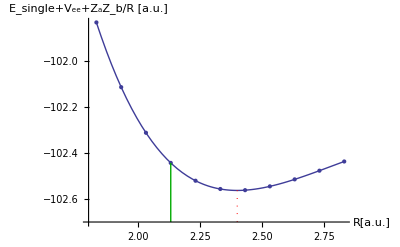

```mathematica
Show[Plot[interpolEnergyR[R],{R,First[Rlist],Last[Rlist]},AxesLabel->{"R[a.u.]","E_single+V_ee+Z_aZ_b/R [a.u.]"},AxesOrigin->{1.8,-102.7}],ListPlot[minEnergyR],Graphics[{Darker[Green],Line[{{Subscript[R, CO],-102.7},minEnergyR⟦4⟧}]}],Graphics[{Dotted,Red,Line[{Emin,{First[Emin],-102.7}}]}]]
```

```mathematica
(* minimum energy at experimental bond length *)
First[Position[Rlist,Subscript[R, CO]]]
minEnergyR⟦%⟧
```

{4}

{{2.13161,-102.443}}

```mathematica
Length[singleEnergy]
```

11

```mathematica
(* eigenvalue gaps *)
First[Position[Rlist,Subscript[R, CO]]]
Differences[Eigenvalues[singleEnergy⟦%⟧+Vee⟦%⟧+Vnn⟦%⟧]⟦1;;6⟧]
```

{4}

{0.62238,0.370156,0.087837,0.0915243,0.134523}

### Bond dissociation energy

```mathematica
(* Explicit large nuclear charge limit of electronic ground states-Friesecke Goddard 2008 *)
−34.4468(* C atom *)-66.7048(* O atom *)
%-{Last[Emin],Last[minEnergyR⟦Position[Rlist,Subscript[R, CO]]⟦1,1⟧⟧]}
```

-101.152

{1.41123,1.29167}

```mathematica
(* 2 h c Ry *)
2PlanckConstant SpeedOfLight RydbergConstant/(ElectronCharge Volt)
eVToAU=First[%]
```

(27.2114 Joule)/(Coulomb Volt)

27.2114

```mathematica
(* experimental bond dissociation energy of CO ("Bond Dissociation Energies in Simple Molecules" by Darwent, 1970) *)
1071.94 10^3 1/(Mole AvogadroConstant) (Coulomb eV)/ElectronCharge
%/eVToAU au/eV
```

11.1099 eV

0.40828 au